# CFD Interior Optimization

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

# First Derivatives

# T2 Scheme

## Coefficient Setup

```mathematica
nL=1; (*Number of interior parameters on the LHS*)
nR=2; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=1; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α};
freePars={a1,a2};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α==2*(a1+2*a2);
(*fixedEq2=2/(2!)*α==2/(3!)*(a1+2^3*a2);*)
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]);
Denom[κ_]=1+2*α*Cos[κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Kim's integrand, Δ^2=(κ-N/D)^2*)
ΔKim22024[κ_]=(κ-Num[κ]/Denom[κ])^2//Together//TrigReduce;
ΔKim2[κ_]=((1+δ)*κ*Denom[κ]-Num[κ])^2*(κ/r)^n;

(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<=1,n∈Integers,δ∈Reals}];
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<=1];
```

```mathematica
EDHConstr=EDH/.Solve[fixedEq1,fixedPars[[1]]][[1]]

(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDHConstr,freePars[[1]]]==0;
freeEq2=D[EDHConstr,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,freeEq1,freeEq2},{α,a1,a2}][[1]]
coeffs//TableForm//N

freeEq1=D[EKim,freePars[[1]]]==0;
freeEq2=D[EKim,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,freeEq1,freeEq2},{α,a1,a2}][[1]]
N[coeffs,15]//TableForm
```

6.34472+6.14943 a1^2+5.81531 a2^2-4.85406 (-1+2 a1+4 a2)+2.22291 (-1+2 a1+4 a2)^2+a2 (3.94515-6.16184 (-1+2 a1+4 a2))+a1 (-11.3315+0.500084 a2+1.97257 (-1+2 a1+4 a2))

{α→0.424594,a1→0.779922,a2→0.0723361}

α→0.424594
a1→0.779922
a2→0.0723361

{α→0.438048,a1→0.766067,a2→0.0859903}

α→0.438048
a1→0.766067
a2→0.0859903

## Results

Optimizing over α and a_1 (with r=2.670/π):
	Our results:
		α→0.418231
a1→0.784465
a2→0.0668833
		
		α→0.424594
a1→0.779922
a2→0.0723361
	Kim’s results:
		N/A

Optimizing over α and a_2 (with r=2.670/π):
	Our results:
		α→0.320406
a1→0.896948
a2→-0.0382708
		
		α→0.424594
a1→0.779922
a2→0.0723361
	Kim’s results:
		N/A

Optimizing over a_1 and a_2 (with r=2.670/π):
	Our results:
		α→0.4099
a1→0.787366
a2→0.0612671
		
		α→0.424594
a1→0.779922
a2→0.0723361
	Kim’s results:
		N/A

## r->π

α and a_1:
	α→0.459341
a1→0.770329
a2→0.0945061
	
	α→0.466988
a1→0.757542
a2→0.104723

α and a_2:
	α→0.494872
a1→0.675214
a2→0.159829
	
	α→0.466988
a1→0.757542
a2→0.104723

a_1 and a_2:
	α→0.428571
a1→0.785714
a2→0.0714286
	
	α→0.466988
a1→0.757542
a2→0.104723

## Visualization

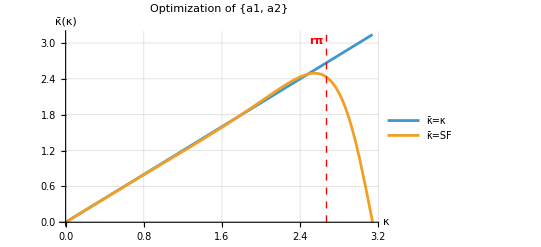

```mathematica
coeffs1={α->0.41823122970441956,a1->0.7844646372810776,a2->0.06688329621167091};
(*coeffs1={α->14/(-9+4 π^2),a1->(4 (-4+π^2))/(-9+4 π^2),a2->-(-51+4 π^2)/(4 (-9+4 π^2))};*)
r1=2.670/π;
coeffs2={α->0.3204064166806459,a1->0.8969479716702151,a2->-0.038270777494784664};
(*coeffs2={α->21/(4 (-19+3 π^2)),a1->-(149-18 π^2)/(4 (-19+3 π^2)),a2->-(3 (-11+π^2))/(2 (-19+3 π^2))};*)
r2=2.670/π;
coeffs3={α->0.40989971396785435,a1->0.7873655261760304,a2->0.061267093895912006};
(*coeffs3={α->3/7,a1->11/14,a2->1/14};*)
r3=2.670/π;

coeffs={α->0.42459428178274977,a1->0.7799221628150456,a2->0.07233605948385209};

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
```

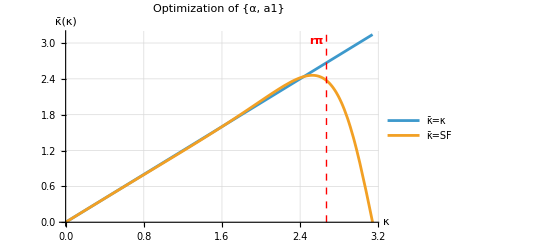

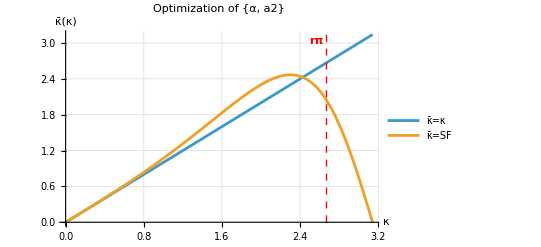

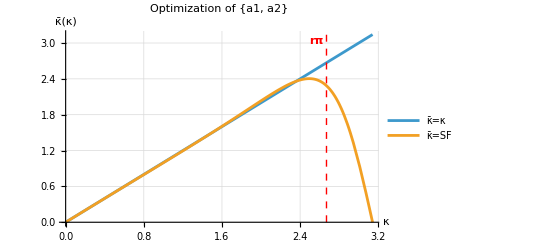

```mathematica
Plot[{κ,κBar[κ]/.coeffs1},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,a1}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r1*π,0},{r1*π,π}}],Text[Style["rπ",Bold],{r1*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs2},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r2*π,0},{r2*π,π}}],Text[Style["rπ",Bold],{r2*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs3},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{a1,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r3*π,0},{r3*π,π}}],Text[Style["rπ",Bold],{r3*π-0.1,π-0.1}]}]
```

## 3D Visualization

```mathematica
EDH3D=EDH/.Solve[fixedEq1,fixedPars[[1]]][[1]]
EDH3DCase1=1/3 π (6 a1^2+π^2+6 a1 (-2+α)-24 α+3 α^2+2 π^2 α^2+1/4 (6-16 α) (1-2 a1+2 α)+3/8 (1-2 a1+2 α)^2);
EDH3DCase2=1/3 π (6 a2^2+π^2+a2 (6-16 α)-24 α+3 α^2+2 π^2 α^2+3 (-2+α) (1-4 a2+2 α)+3/2 (1-4 a2+2 α)^2);
EDH3DCase3=1/3 π (6 a1^2+6 a2^2-12 (-1+2 a1+4 a2)+3/4 (-1+2 a1+4 a2)^2+a2 (6-8 (-1+2 a1+4 a2))+6 a1 (-2+1/2 (-1+2 a1+4 a2))+π^2+1/2 (-1+2 a1+4 a2)^2 π^2);
(*Plot3D[EDH3D,{a1,-1,1},{α,-1,1}]*)


Plot3D[EDH3DCase1,{a1,-1,1},{α,-1,1}]
Plot3D[EDH3DCase2,{a2,-1,1},{α,-1,1}]
Plot3D[EDH3DCase3,{a1,-1,1},{a2,-1,1}]
```

1/3 π (6 a1^2+6 a2^2-12 (-1+2 a1+4 a2)+3/4 (-1+2 a1+4 a2)^2+a2 (6-8 (-1+2 a1+4 a2))+6 a1 (-2+1/2 (-1+2 a1+4 a2))+π^2+1/2 (-1+2 a1+4 a2)^2 π^2)

-Graphics3D-

-Graphics3D-

-Graphics3D-

# P4 (A4) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Kim's integrand, Δ^2=(κ-N/D)^2*)
ΔKim22024[κ_]=(κ-Num[κ]/Denom[κ])^2//Together//TrigReduce;
ΔKim2[κ_]=((1+δ)*κ*Denom[κ]-Num[κ])^2*(κ/r)^n;

(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
(*EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<1,n∈Integers,δ∈Reals}];*)
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
```

```mathematica
EDHConstr=EDH/.Solve[{fixedEq1,fixedEq2},{fixedPars[[1]],fixedPars[[2]]}][[1]];

(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDHConstr,freePars[[1]]]==0;
freeEq2=D[EDHConstr,freePars[[2]]]==0;
freeEq3=D[EDHConstr,freePars[[3]]]==0;

coeffsNateP4=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsNateP4//TableForm

freeEq1=D[EKim,freePars[[1]]]==0;
freeEq2=D[EKim,freePars[[2]]]==0;
freeEq3=D[EKim,freePars[[3]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
N[coeffs,15]//TableForm
```

{α→0.577046,β→0.0890084,a1→0.651708,a2→0.248159,a3→0.00600963}

α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963

Solve::svars: Equations may not give solutions for all "solve" variables.

{a2→9/20-(4 a1)/5+(3 α)/5-(3 β)/10,a3→-2/15+a1/5-α/15+(8 β)/15}

a2→0.45-0.8 a1+0.6 α-0.3 β
a3→-0.133333333333333+0.2 a1-0.0666666666666667 α+0.533333333333333 β

```mathematica
ELowNateA4=Integrate[(ΔDH2[κ])/.coeffsNateP4,{κ,0,r π}];
ScientificForm@ELowNateA4

ETotNateA4=Integrate[(ΔDH2[κ])/.coeffsNateP4,{κ,0,π}];
ScientificForm@ETotNateA4
```

3.33808×10^-7

5.09089×10^-4

```mathematica
ELowNateA6=Integrate[(ΔDH2[κ])/.coeffs,{κ,0,r π}];
ScientificForm@ELowNateA6

ETotNateA6=Integrate[(ΔDH2[κ])/.coeffs,{κ,0,π}];
ScientificForm@ETotNateA6
```

2.96587×10^-6

1.49539×10^-3

## Spectral

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};
(*This should be the same length as freePars*)
κConstrA41st={2.4,2.6,2.8};
```

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num[κConstrA41st[[1]]]==(κConstrA41st[[1]])*Denom[κConstrA41st[[1]]];
freeEq2=Num[κConstrA41st[[2]]]==(κConstrA41st[[2]])*Denom[κConstrA41st[[2]]];
freeEq3=Num[κConstrA41st[[3]]]==(κConstrA41st[[3]])*Denom[κConstrA41st[[3]]];

coeffsTylerA41st=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsTylerA41st//TableForm
```

{α→0.524845,β→0.0632013,a1→0.148951,a2→0.453071,a3→0.023873}

α→0.524845
β→0.0632013
a1→0.148951
a2→0.453071
a3→0.023873

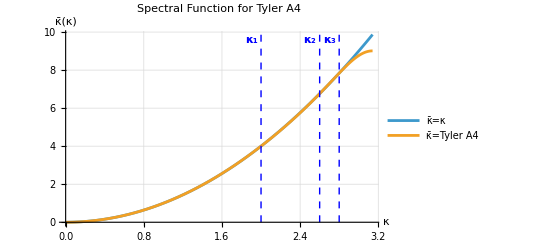

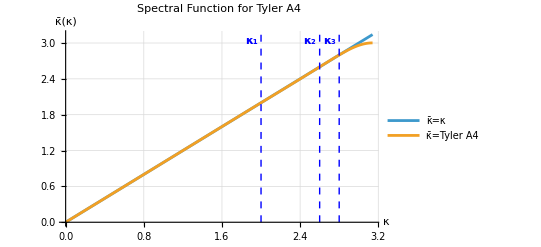

```mathematica
Plot[{κ^2,κBar[κ]/.coeffsTylerA42nd},{κ,0,π},PlotRange->{0,π^2},PlotLabel->"Spectral Function for Tyler A4",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A4"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA42nd[[1]],0},{κConstrA42nd[[1]],π^2}}],Text[Style["κ_1",Bold],{κConstrA42nd[[1]]-0.1,π^2-0.3}],Line[{{κConstrA42nd[[2]],0},{κConstrA42nd[[2]],π^2}}],Text[Style["κ_2",Bold],{κConstrA42nd[[2]]-0.1,π^2-0.3}],Line[{{κConstrA42nd[[3]],0},{κConstrA42nd[[3]],π^2}}],Text[Style["κ_3",Bold],{κConstrA42nd[[3]]-0.1,π^2-0.3}]}]
Plot[{κ,Sqrt[κBar[κ]/.coeffsTylerA42nd]},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Tyler A4",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A4"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA42nd[[1]],0},{κConstrA42nd[[1]],π}}],Text[Style["κ_1",Bold],{κConstrA42nd[[1]]-0.1,π-0.1}],Line[{{κConstrA42nd[[2]],0},{κConstrA42nd[[2]],π}}],Text[Style["κ_2",Bold],{κConstrA42nd[[2]]-0.1,π-0.1}],Line[{{κConstrA42nd[[3]],0},{κConstrA42nd[[3]],π}}],Text[Style["κ_3",Bold],{κConstrA42nd[[3]]-0.1,π-0.1}]}]
```

### Error comparison with Kim-style optimization

```mathematica
r=2.670/π;

ELowNateA4=Integrate[(ΔDH2[κ])/.coeffsNateA42nd,{κ,0,r*π}];
ELowTylerA4=Integrate[(ΔDH2[κ])/.coeffsTylerA42nd,{κ,0,r*π}];

ETotNateA4=Integrate[(ΔDH2[κ])/.coeffsNateA42nd,{κ,0,π}];
ETotTylerA4=Integrate[(ΔDH2[κ])/.coeffsTylerA42nd,{κ,0,π}];

Print[
"Integrated error for low wavenumber (κ≤rπ):\n",
TableForm[{
{"Nate P4:",ScientificForm@ELowNateA4},
{"Tyler A4:",ScientificForm@ELowTylerA4}
}]]
Print[
"Integrated total error:\n",
TableForm[{
{"Nate P4:",ScientificForm@ETotNateA4},
{"Tyler A4:",ScientificForm@ETotTylerA4}
}]]
```

Integrated error for low wavenumber (κ≤rπ):
Nate P4: | 4.49717×10^-7
Tyler A4: | 4.72932×10^-6

Integrated total error:
Nate P4: | 1.58551×10^-3
Tyler A4: | 2.65021×10^-4

## Visualization

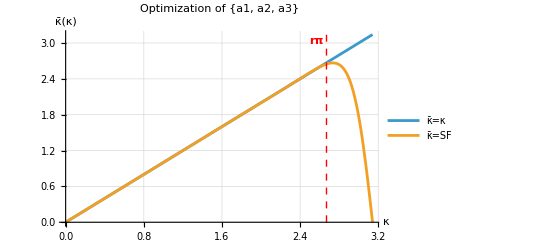

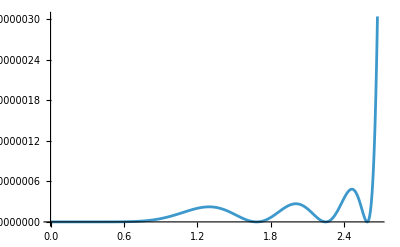

```mathematica
coeffs1={α->0.5674984766667983,β->0.08270928003870921,a1->0.6603882207694884,a2->0.23737572537287543,a3->0.005022695063422676};
r1=2.661/π;
coeffs2={α->0.5698649252859338,β->0.08422366118619422,a1->0.6582794461943285,a2->0.24002829986023835,a3->0.005250846852440635};
r2=2.671/π;
coeffs3={α->0.46212528854158036,β->0.01433680907756551,a1->0.7545208706724549,a2->0.11935743386371474,a3->-0.0055912135935795295};
r3=2.669/π;
coeffs4={α->0.5843384783205174,β->0.09375348681411781,a1->0.6451457202668986,a2->0.2563604647345564,a3->0.00674177179954127};
r4=2.672/π;

coeffsCor={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};
rCor=2.670/π;
Plot[{κ,κBar[κ]/.coeffsCor},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π}}],Text[Style["rπ",Bold],{rCor*π-0.1,π-0.1}]}]

Plot[ΔDH2[κ]/.coeffsCor,{κ,0,r π},PlotRange->All]

(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
```

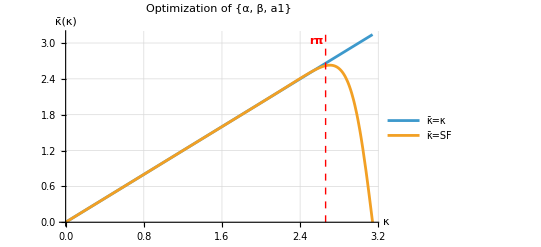

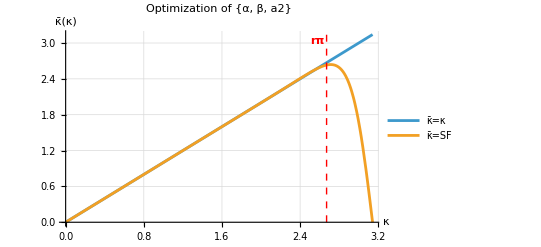

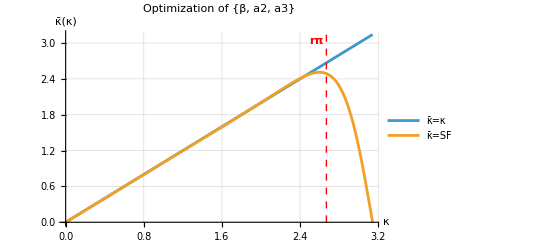

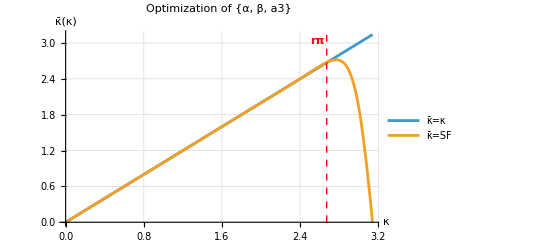

```mathematica
Plot[{κ,κBar[κ]/.coeffs1},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a1}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r1*π,0},{r1*π,π}}],Text[Style["rπ",Bold],{r1*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs2},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r2*π,0},{r2*π,π}}],Text[Style["rπ",Bold],{r2*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs3},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{β,a2,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r3*π,0},{r3*π,π}}],Text[Style["rπ",Bold],{r3*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r4*π,0},{r4*π,π}}],Text[Style["rπ",Bold],{r4*π-0.1,π-0.1}]}]
```

## Extra Stuff

### Results

Optimizing over α, β, and a_1 (with r=2.661/π):
	Our results:
		α→0.567498
β→0.0827093
a1→0.660388
a2→0.237376
a3→0.0050227
	Kim’s results:
		α->0.5856396845642288
β->0.09505833117193530
a_1->0.6437151795729501
a_2->0.2578941677285964
a_3->0.007064833568673624

Optimizing over α, β and a_2 (with r=2.671/π):
	Our results:
		α→0.569865
β→0.0842237
a1→0.658279
a2→0.240028
a3→0.00525085
	Kim’s results:
		α->0.5859572811123209
β->0.09527180900906593
a_1->0.6434288190645918
a_2->0.2582497707129994
a_3->0.007100243210265430

Optimizing over β, a_2, and a_3 (with r=2.669/π):
	Our results:
		α→0.462125
β→0.0143368
a1→0.754521
a2→0.119357
a3→-0.00559121
	Kim’s results:
		α->0.5864696980962217
β->0.09564623994911990
a_1->0.6429512471438849
a_2->0.2588269491578893
a_3->0.007170264195226098

Optimizing over α, β, and a_3 (with r=2.672/π):
	Our results:
		α→0.584338
β→0.0937535
a1→0.645146
a2→0.25636
a3→0.00674177
	Kim’s results:
		α->0.5862704032801503
β->0.09549533555017055
a_1->0.6431406736919156
a_2->0.2586011023495066
a_3->0.007140953479797375


Correct results (r=2.670):
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963

### Zoomed In Plots

-Graphics-

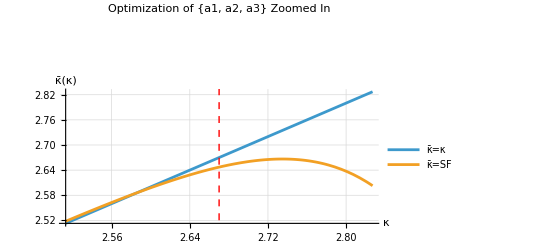

```mathematica
(*ϵ is the zoom factor; the zoomed plot will go from (r-ϵ)π to (r+ϵ)π*)
ϵ=0.05;

Plot[{κ,κBar[κ]/.coeffsCor},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π}}],Text[Style["rπ",Bold],{rCor*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffsCor},{κ,(rCor-ϵ)*π,(rCor+ϵ)*π},PlotRange->{(rCor-ϵ)*π,(rCor+ϵ)*π},PlotLabel->"Optimization of "<>ToString[freePars]<>"\nZoomed In",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π}}],Text[Style["rπ",Bold],{rCor*π-0.05,π-0.2}]}]
```

### Varying r Values

```mathematica
ΔDH2[κ];
Clear[EDH,𝓇]
EDH[𝓇_]=Integrate[ΔDH2[κ],{κ,0,𝓇*π}]/.coeffs4
totError=EDH[1]
```

3.02836 𝓇+17.5752 𝓇^3+5.66594 𝓇 Cos[2 π 𝓇]+1.06207 𝓇 Cos[3 π 𝓇]+0.0947869 𝓇 Cos[4 π 𝓇]+0.00158855 𝓇 Cos[5 π 𝓇]+Cos[π 𝓇] (25.3004 𝓇-0.341451 Sin[π 𝓇])-7.38488 Sin[π 𝓇]+25.2315 𝓇^2 Sin[π 𝓇]-1.13855 Sin[2 π 𝓇]+5.22061 𝓇^2 Sin[2 π 𝓇]-0.333209 Sin[3 π 𝓇]+0.720926 𝓇^2 Sin[3 π 𝓇]-0.0447527 Sin[4 π 𝓇]+0.0433755 𝓇^2 Sin[4 π 𝓇]-0.00148379 Sin[5 π 𝓇]-0.0000151505 Sin[6 π 𝓇]

0.000281384

```mathematica
(*D[EDH[r4],freePars[[1]]]
D[EDH[r4],freePars[[2]]]
D[EDH[r4],freePars[[3]]]*)
```

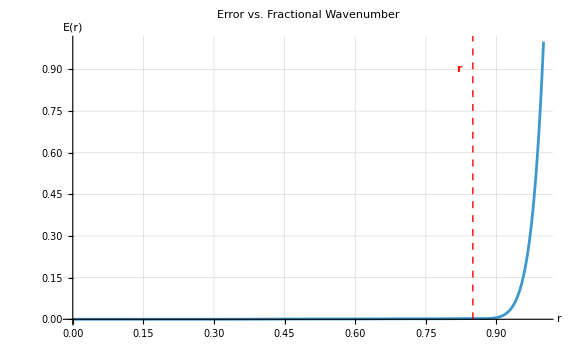

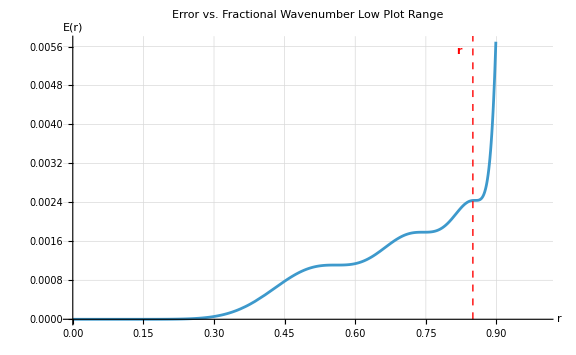

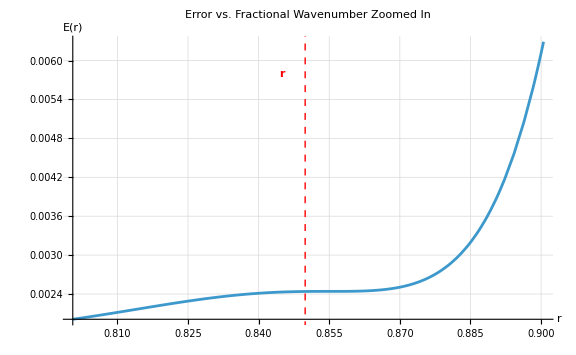

-Graphics-

-Graphics-

```mathematica
Plot[1/totError EDH[𝓇],{𝓇,0,1},PlotRange->All,PlotLabel->"Error vs. Fractional Wavenumber",AxesLabel->{"r","E(r)"},GridLines->Automatic,Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r,0},{r,1.5}}],Text[Style["r",Bold],{r-0.03,0.9}]},ImageSize->Large]
Plot[1/totError EDH[𝓇],{𝓇,0,1},PlotLabel->"Error vs. Fractional Wavenumber\nLow Plot Range",AxesLabel->{"r","E(r)"},GridLines->Automatic,Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r,0},{r,1.5}}],Text[Style["r",Bold],{r-0.03,0.0055}]},ImageSize->Large]
Plot[1/totError EDH[𝓇],{𝓇,r4-ϵ,r4+ϵ},PlotRange->All,PlotLabel->"Error vs. Fractional Wavenumber\nZoomed In",AxesLabel->{"r","E(r)"},GridLines->Automatic,Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r,0},{r,1.5}}],Text[Style["r",Bold],{r-0.005,0.0058}]},ImageSize->Large]
```

### Convergence as r->1?

```mathematica
Clear[r]
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1]
```

2 a1^2 π r+2 a2^2 π r+2 a3^2 π r+(π^3 r^3)/3+2/3 π^3 r^3 α^2+2/3 π^3 r^3 β^2+4 π r (a1-a1 β+a3 β+α (2+a2+2 β)) Cos[π r]+π r (2 a2+2 a1 α+2 a3 α+α^2+2 β) Cos[2 π r]+4/3 a3 π r Cos[3 π r]+4/3 a2 π r α Cos[3 π r]+4/3 a1 π r β Cos[3 π r]+8/9 π r α β Cos[3 π r]+a3 π r α Cos[4 π r]+a2 π r β Cos[4 π r]+1/4 π r β^2 Cos[4 π r]+4/5 a3 π r β Cos[5 π r]-4 a1 Sin[π r]+4 a1 a2 Sin[π r]+4 a2 a3 Sin[π r]-8 α Sin[π r]-4 a2 α Sin[π r]+4 π^2 r^2 α Sin[π r]+4 a1 β Sin[π r]-4 a3 β Sin[π r]-8 α β Sin[π r]+4 π^2 r^2 α β Sin[π r]-a1^2 Sin[2 π r]-a2 Sin[2 π r]+2 a1 a3 Sin[2 π r]-a1 α Sin[2 π r]-a3 α Sin[2 π r]-1/2 α^2 Sin[2 π r]+π^2 r^2 α^2 Sin[2 π r]-β Sin[2 π r]+2 π^2 r^2 β Sin[2 π r]-4/3 a1 a2 Sin[3 π r]-4/9 a3 Sin[3 π r]-4/9 a2 α Sin[3 π r]-4/9 a1 β Sin[3 π r]-8/27 α β Sin[3 π r]+4/3 π^2 r^2 α β Sin[3 π r]-1/2 a2^2 Sin[4 π r]-a1 a3 Sin[4 π r]-1/4 a3 α Sin[4 π r]-1/4 a2 β Sin[4 π r]-1/16 β^2 Sin[4 π r]+1/2 π^2 r^2 β^2 Sin[4 π r]-4/5 a2 a3 Sin[5 π r]-4/25 a3 β Sin[5 π r]-1/3 a3^2 Sin[6 π r]

```mathematica
𝓇=π/π;

fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
freeEq1=D[EDH/.{r->𝓇},freePars[[1]]]==0;
freeEq2=D[EDH/.{r->𝓇},freePars[[2]]]==0;
freeEq3=D[EDH/.{r->𝓇},freePars[[3]]]==0;
coeffs=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]];
coeffs//TableForm//N
```

α→0.581818
β→0.0909091
a1→0.648485
a2→0.25303
a3→0.00606061

Here are the coefficients when r=1:

Case 1:
	α→0.588784
β→0.0943795
a1→0.642688
a2→0.260806
a3→0.00628782

Case 2:
	α→0.601903
β→0.105194
a1→0.629181
a2→0.276238
a3→0.00847945

Case 3:
	α→0.607947
β→0.110145
a1→0.623331
a2→0.283059
a3→0.00954708

Case 4:
	α→0.606623
β→0.109085
a1→0.624321
a2→0.281791
a3→0.00926799

Case 5:
	α→0.581818
β→0.0909091
a1→0.648485
a2→0.25303
a3→0.00606061

# P4 (B4) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=4; (*Number of interior parameters on the RHS*)
nF=4; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF) (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3,a4};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

4

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3+4*a4);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3+4^3*a4);



(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]+a4*Sin[4*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];



(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];



(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDH,freePars[[1]]]==0;
freeEq2=D[EDH,freePars[[2]]]==0;
freeEq3=D[EDH,freePars[[3]]]==0;
freeEq4=D[EDH,freePars[[4]]]==0;

coeffsB4=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3,freeEq4},{α,β,a1,a2,a3,a4}][[1]]
coeffsB4//TableForm
```

{α→0.594235,β→0.102757,a1→0.634047,a2→0.267266,a3→0.0100472,a4→-0.000432113}

α→0.594235
β→0.102757
a1→0.634047
a2→0.267266
a3→0.0100472
a4→-0.000432113

## Visualization

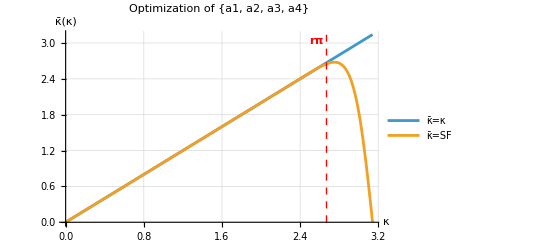

```mathematica
(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
Plot[{κ,κBar[κ]/.coeffsB4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

# P4 (C4) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=2; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF) (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={β,a1};
freePars={α,a2};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

4

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2);



(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];



(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];



(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDH,freePars[[1]]]==0;
freeEq2=D[EDH,freePars[[2]]]==0;

coeffsC4=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2},{α,β,a1,a2}][[1]]
coeffsC4//TableForm
```

{α→0.536293,β→0.058317,a1→0.689919,a2→0.202345}

α→0.536293
β→0.058317
a1→0.689919
a2→0.202345

## Visualization

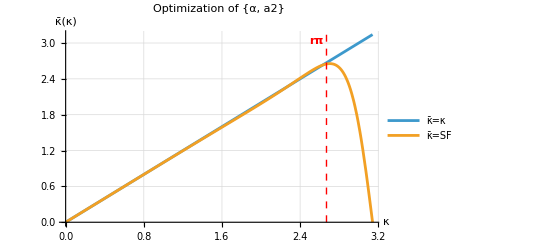

```mathematica
(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
Plot[{κ,κBar[κ]/.coeffsC4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

# P6 (A6) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β,a1};
freePars={a2,a3};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
fixedEq3=2/(4!)*(α+2^4*β)==2/(5!)*(a1+2^5*a2+3^5*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
(*EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<1,n∈Integers,δ∈Reals}];*)
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDH,freePars[[1]]]==0;
freeEq2=D[EDH,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2},{α,β,a1,a2,a3}][[1]]
coeffs//TableForm
```

{α→0.557322,β→0.0762035,a1→0.669438,a2→0.225982,a3→0.00404124}

α→0.557322
β→0.0762035
a1→0.669438
a2→0.225982
a3→0.00404124

## Results

Optimizing over α and β (with r=2.670/π):
	Our results:
		α→0.5589
β→0.0770111
a1→0.668223
a2→0.227658
a3→0.0041239
	Kim’s results:
		N/A

Optimizing over β and a_1 (with r=2.670/π):
	Our results:
		α→0.559064
β→0.0770179
a1→0.668225
a2→0.227753
a3→0.00411705
	Kim’s results:
		N/A

Optimizing over β and a_2 (with r=2.670/π):
	Our results:
		α→0.558736
β→0.0770044
a1→0.668221
a2→0.227564
a3→0.00413072
	Kim’s results:
		N/A

Optimizing over β and a_3 (with r=2.670/π):
	Our results:
		α→0.558562
β→0.0769971
a1→0.668218
a2→0.227464
a3→0.00413798
	Kim’s results:
		N/A

Optimizing over α and a_1 (with r=2.670/π):
	Our results:
		α→0.556885
β→0.075843
a1→0.670002
a2→0.225376
a3→0.00399103
	Kim’s results:
		N/A

Optimizing over α and a_2 (with r=2.670/π):
	Our results:
		α→0.565356
β→0.0807533
a1→0.662524
a2→0.234968
a3→0.00454953
	Kim’s results:
		N/A

Optimizing over α and a_3 (with r=2.670/π):
	Our results:
		α→0.555557
β→0.0750732
a1→0.671174
a2→0.223872
a3→0.00390347
	Kim’s results:
		N/A

Optimizing over a_1 and a_2 (with r=2.670/π):
	Our results:
		α→0.552751
β→0.0736146
a1→0.673372
a2→0.220869
a3→0.00375202
	Kim’s results:
		N/A

Optimizing over a_1 and a_3 (with r=2.670/π):
	Our results:
		α→0.556089
β→0.0754143
a1→0.67065
a2→0.224509
a3→0.00394505
	Kim’s results:
		N/A

Optimizing over a_2 and a_3 (with r=2.670/π):
	Our results:
		α→0.557322
β→0.0762035
a1→0.669438
a2→0.225982
a3→0.00404124
	Kim’s results:
		N/A

## Visualization

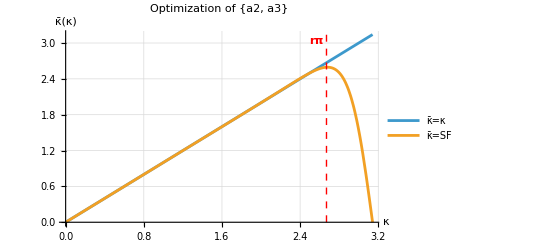

```mathematica
(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

# P6 (B6) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=4; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β,a1};
freePars={a2,a3,a4};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3+4*a4);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3+4^3*a4);
fixedEq3=2/(4!)*(α+2^4*β)==2/(5!)*(a1+2^5*a2+3^5*a3+4^5*a4);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]+a4*Sin[4*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Kim's integrand, Δ^2=(κ-N/D)^2*)
ΔKim22024[κ_]=(κ-Num[κ]/Denom[κ])^2//Together//TrigReduce;
ΔKim2[κ_]=((1+δ)*κ*Denom[κ]-Num[κ])^2*(κ/r)^n;

(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
(*EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<1,n∈Integers,δ∈Reals}];*)
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDH,freePars[[1]]]==0;
freeEq2=D[EDH,freePars[[2]]]==0;
freeEq3=D[EDH,freePars[[3]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3,a4}][[1]]
coeffs//TableForm

(*freeEq1=D[EKim,freePars[[1]]]==0;
freeEq2=D[EKim,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2},{α,β,a1,a2,a3}][[1]]
N[coeffs,15]//TableForm*)
```

{α→0.590671,β→0.100051,a1→0.637598,a2→0.263284,a3→0.00934037,a4→-0.000366182}

α→0.590671
β→0.100051
a1→0.637598
a2→0.263284
a3→0.00934037
a4→-0.000366182

## Results

Optimizing over α and β (with r=2.670/π):
	Our results:
		α→0.5589
β→0.0770111
a1→0.668223
a2→0.227658
a3→0.0041239
	Kim’s results:
		N/A

Optimizing over β and a_1 (with r=2.670/π):
	Our results:
		α→0.559064
β→0.0770179
a1→0.668225
a2→0.227753
a3→0.00411705
	Kim’s results:
		N/A

Optimizing over β and a_2 (with r=2.670/π):
	Our results:
		α→0.558736
β→0.0770044
a1→0.668221
a2→0.227564
a3→0.00413072
	Kim’s results:
		N/A

Optimizing over β and a_3 (with r=2.670/π):
	Our results:
		α→0.558562
β→0.0769971
a1→0.668218
a2→0.227464
a3→0.00413798
	Kim’s results:
		N/A

Optimizing over α and a_1 (with r=2.670/π):
	Our results:
		α→0.556885
β→0.075843
a1→0.670002
a2→0.225376
a3→0.00399103
	Kim’s results:
		N/A

Optimizing over α and a_2 (with r=2.670/π):
	Our results:
		α→0.565356
β→0.0807533
a1→0.662524
a2→0.234968
a3→0.00454953
	Kim’s results:
		N/A

Optimizing over α and a_3 (with r=2.670/π):
	Our results:
		α→0.555557
β→0.0750732
a1→0.671174
a2→0.223872
a3→0.00390347
	Kim’s results:
		N/A

Optimizing over a_1 and a_2 (with r=2.670/π):
	Our results:
		α→0.552751
β→0.0736146
a1→0.673372
a2→0.220869
a3→0.00375202
	Kim’s results:
		N/A

Optimizing over a_1 and a_3 (with r=2.670/π):
	Our results:
		α→0.556089
β→0.0754143
a1→0.67065
a2→0.224509
a3→0.00394505
	Kim’s results:
		N/A

Optimizing over a_2 and a_3 (with r=2.670/π):
	Our results:
		α→0.557322
β→0.0762035
a1→0.669438
a2→0.225982
a3→0.00404124
	Kim’s results:
		N/A

## Visualization

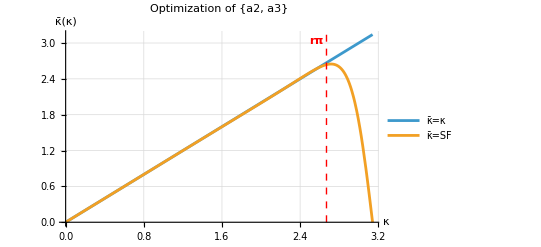

```mathematica
coeffs1={α->0.5674984766667983,β->0.08270928003870921,a1->0.6603882207694884,a2->0.23737572537287543,a3->0.005022695063422676};
r1=2.661/π;
coeffs2={α->0.5698649252859338,β->0.08422366118619422,a1->0.6582794461943285,a2->0.24002829986023835,a3->0.005250846852440635};
r2=2.671/π;
coeffs3={α->0.46212528854158036,β->0.01433680907756551,a1->0.7545208706724549,a2->0.11935743386371474,a3->-0.0055912135935795295};
r3=2.669/π;
coeffs4={α->0.5843384783205174,β->0.09375348681411781,a1->0.6451457202668986,a2->0.2563604647345564,a3->0.00674177179954127};
r4=2.672/π;


(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

```mathematica
Plot[{κ,κBar[κ]/.coeffs1},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a1}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r1*π,0},{r1*π,π}}],Text[Style["rπ",Bold],{r1*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs2},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r2*π,0},{r2*π,π}}],Text[Style["rπ",Bold],{r2*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs3},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{β,a2,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r3*π,0},{r3*π,π}}],Text[Style["rπ",Bold],{r3*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r4*π,0},{r4*π,π}}],Text[Style["rπ",Bold],{r4*π-0.1,π-0.1}]}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

# P6 (C6) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=2; (*Number of interior parameters on the RHS*)
nF=1; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF) (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={β,a1,a2};
freePars={α};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

6

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2);
fixedEq3=2/(4!)*(α+2^4*β)==2/(5!)*(a1+2^5*a2);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
(*EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<1,n∈Integers,δ∈Reals}];*)
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDH,freePars[[1]]]==0;

coeffsC6=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1},{α,β,a1,a2}][[1]]
coeffsC6//TableForm
```

{α→0.496348,β→0.0407536,a1→0.72344,a2→0.156831}

α→0.496348
β→0.0407536
a1→0.72344
a2→0.156831

## Visualization

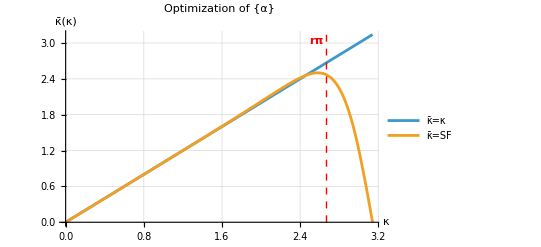

```mathematica
(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
Plot[{κ,κBar[κ]/.coeffsC6},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

# P8 (A8) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=1; (*Number of free parameters*)
nX=4; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β,a1,a2};
freePars={a3};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
fixedEq3=2/(4!)*(α+2^4*β)==2/(5!)*(a1+2^5*a2+3^5*a3);
fixedEq4=2/(6!)*(α+2^6*β)==2/(7!)*(a1+2^7*a2+3^7*a3);
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
EDHConstr=EDH/.Solve[{fixedEq1,fixedEq2,fixedEq3,fixedEq4},{fixedPars[[1]],fixedPars[[2]],fixedPars[[3]],fixedPars[[4]]}][[1]];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDHConstr,freePars[[1]]]==0;

coeffsA81st=Solve[{fixedEq1,fixedEq2,fixedEq3,fixedEq4,freeEq1},{α,β,a1,a2,a3}][[1]]
coeffsA81st//TableForm
```

{α→0.541269,β→0.0665078,a1→0.684259,a2→0.207402,a3→0.00290475}

α→0.541269
β→0.0665078
a1→0.684259
a2→0.207402
a3→0.00290475

# Spectral Schemes

## Tyler Spectral Schemes

### P4 (A4)

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};
(*This should be the same length as freePars*)
κConstrA4={2.0,2.6,2.8};
```

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num[κConstrA4[[1]]]==κConstrA4[[1]]*Denom[κConstrA4[[1]]];
freeEq2=Num[κConstrA4[[2]]]==κConstrA4[[2]]*Denom[κConstrA4[[2]]];
freeEq3=Num[κConstrA4[[3]]]==κConstrA4[[3]]*Denom[κConstrA4[[3]]];

coeffsTylerA4=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsTylerA4//TableForm
```

{α→0.600106,β→0.105301,a1→0.630141,a2→0.27436,a3→0.0088484}

α→0.600106
β→0.105301
a1→0.630141
a2→0.27436
a3→0.0088484

### P6 (A6)

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β,a1};
freePars={a1,a2,a3};
(*This should be the same length as freePars*)
κConstrA6={2.464,2.7171};
```

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
fixedEq3=2/(4!)*(α+2^4*β)==2/(5!)*(a1+2^5*a2+3^5*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num[κConstrA6[[1]]]==κConstrA6[[1]]*Denom[κConstrA6[[1]]];
freeEq2=Num[κConstrA6[[2]]]==κConstrA6[[2]]*Denom[κConstrA6[[2]]];

coeffsTylerA6=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2},{α,β,a1,a2,a3}][[1]]
coeffsTylerA6//TableForm
```

{α→0.579095,β→0.0890519,a1→0.649838,a2→0.250871,a3→0.0055223}

α→0.579095
β→0.0890519
a1→0.649838
a2→0.250871
a3→0.0055223

### P6 (B6)

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=4; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β,a1};
freePars={a2,a3,a4};
(*This should be the same length as freePars*)
κConstrB6={2.3,2.6,2.8};
```

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3+4*a4);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3+4^3*a4);
fixedEq3=2/(4!)*(α+2^4*β)==2/(5!)*(a1+2^5*a2+3^5*a3+4^5*a4);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num2[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]+a4*Sin[4*κ]);
Denom2[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar2[κ_]=Num2[κ]/Denom2[κ];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num2[κConstrB6[[1]]]==κConstrB6[[1]]*Denom2[κConstrB6[[1]]];
freeEq2=Num2[κConstrB6[[2]]]==κConstrB6[[2]]*Denom2[κConstrB6[[2]]];
freeEq3=Num2[κConstrB6[[3]]]==κConstrB6[[3]]*Denom2[κConstrB6[[3]]];

coeffsTylerB6=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3,a4}][[1]]
coeffsTylerB6//TableForm
```

{α→0.616909,β→0.120106,a1→0.611796,a2→0.292563,a3→0.0143701,a4→-0.000754597}

α→0.616909
β→0.120106
a1→0.611796
a2→0.292563
a3→0.0143701
a4→-0.000754597

### Hybrid A42K1T

{α→0.594588,β→0.100932,a1→0.635567,a2→0.268019,a3→0.00797153}

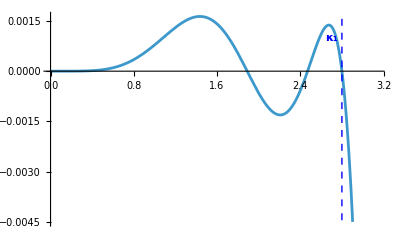

Low error: 2.13957×10^-6

Total error: 1.07712×10^-4

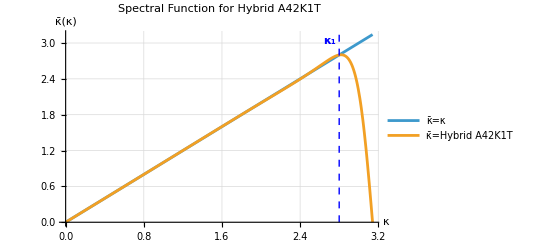

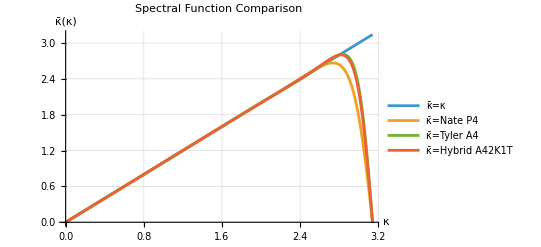

```mathematica
(*=========SECTION 1=========*)
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};
(*This should be the same length as freePars*)
κConstrA4={2.8};

(*=========SECTION 2=========*)
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)

(*=========SECTION 3=========*)
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];

(*=========SECTION 4=========*)
(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
EDHConstr=EDH/.Solve[{fixedEq1,fixedEq2},{fixedPars[[1]],fixedPars[[2]]}][[1]];

(*=========SECTION 5=========*)
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num[κConstrA4[[1]]]==κConstrA4[[1]]*Denom[κConstrA4[[1]]];

freeEq2=D[EDHConstr,freePars[[1]]]==0;
freeEq3=D[EDHConstr,freePars[[2]]]==0;

coeffsTylerA42K1T=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsTylerA42K1T//TableForm;

(*=========SECTION 6=========*)
Plot[(Num[κ]-κ*Denom[κ])/.coeffsTylerA42K1T,{κ,0,π},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA4[[1]],-1},{κConstrA4[[1]],1}}],Text[Style["κ_1",Bold],{κConstrA4[[1]]-0.1,0.001}]}]
Print["Low error: ",ScientificForm@Integrate[(ΔDH2[κ])/.coeffsTylerA42K1T,{κ,0,r*π}]]
Print["Total error: ",ScientificForm@Integrate[(ΔDH2[κ])/.coeffsTylerA42K1T,{κ,0,π}]]
Plot[{κ,κBar[κ]/.coeffsTylerA42K1T},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Hybrid A42K1T",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Hybrid A42K1T"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA4[[1]],0},{κConstrA4[[1]],π}}],Text[Style["κ_1",Bold],{κConstrA4[[1]]-0.1,π-0.1}]}]
Plot[{κ,κBar[κ]/.coeffsNateP4,κBar[κ]/.coeffsTylerA4,κBar[κ]/.coeffsTylerA42K1T},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function Comparison",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Nate P4","κ̄=Tyler A4","κ̄=Hybrid A42K1T"}]
```

### Hybrid A41K2T

{α→0.600798,β→0.105889,a1→0.629521,a2→0.275095,a3→0.00899188}

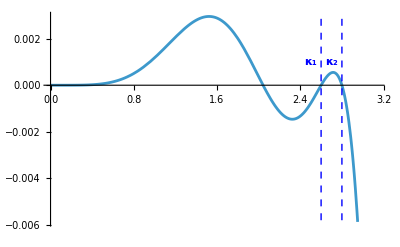

Low error: 5.83334×10^-6

Total error: 6.97192×10^-5

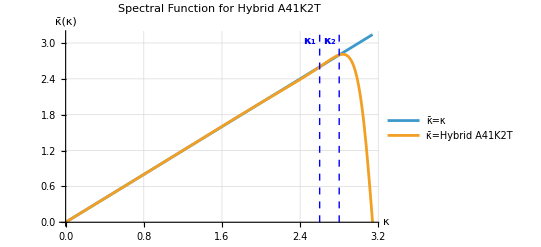

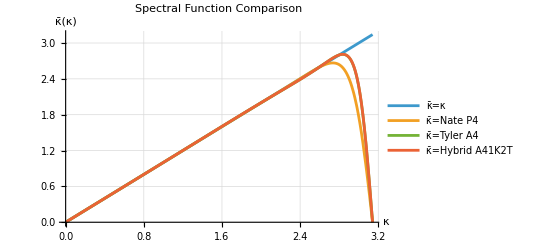

```mathematica
(*=========SECTION 1=========*)
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};
(*This should be the same length as freePars*)
κConstrA4={2.6,2.8};

(*=========SECTION 2=========*)
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)

(*=========SECTION 3=========*)
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];

(*=========SECTION 4=========*)
(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
EDHConstr=EDH/.Solve[{fixedEq1,fixedEq2},{fixedPars[[1]],fixedPars[[2]]}][[1]];

(*=========SECTION 5=========*)
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num[κConstrA4[[1]]]==κConstrA4[[1]]*Denom[κConstrA4[[1]]];
freeEq2=Num[κConstrA4[[2]]]==κConstrA4[[2]]*Denom[κConstrA4[[2]]];

freeEq3=D[EDHConstr,freePars[[1]]]==0;

coeffsTylerA41K2T=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsTylerA41K2T//TableForm;

(*=========SECTION 6=========*)
Plot[(Num[κ]-κ*Denom[κ])/.coeffsTylerA41K2T,{κ,0,π},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA4[[1]],-1},{κConstrA4[[1]],1}}],Text[Style["κ_1",Bold],{κConstrA4[[1]]-0.1,0.001}],Line[{{κConstrA4[[2]],-1},{κConstrA4[[2]],1}}],Text[Style["κ_2",Bold],{κConstrA4[[2]]-0.1,0.001}]}]
Print["Low error: ",ScientificForm@Integrate[(ΔDH2[κ])/.coeffsTylerA41K2T,{κ,0,r*π}]]
Print["Total error: ",ScientificForm@Integrate[(ΔDH2[κ])/.coeffsTylerA41K2T,{κ,0,π}]]
Plot[{κ,κBar[κ]/.coeffsTylerA41K2T},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Hybrid A41K2T",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Hybrid A41K2T"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA4[[1]],0},{κConstrA4[[1]],π}}],Text[Style["κ_1",Bold],{κConstrA4[[1]]-0.1,π-0.1}],Line[{{κConstrA4[[2]],0},{κConstrA4[[2]],π}}],Text[Style["κ_2",Bold],{κConstrA4[[2]]-0.1,π-0.1}]}]
Plot[{κ,κBar[κ]/.coeffsNateP4,κBar[κ]/.coeffsTylerA4,κBar[κ]/.coeffsTylerA41K2T},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function Comparison",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Nate P4","κ̄=Tyler A4","κ̄=Hybrid A41K2T"}]
```

### Hybrid A6

### Hybrid B6

### Error comparison with Kim-style optimization

```mathematica
r=2.670/π;

ΔDH2A[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;
ΔDH2B[κ_]=(κ*Denom2[κ]-Num2[κ])^2//Expand;
(*ETotA=Integrate[ΔDH2A[κ],{κ,0,π}]
ETotB=Integrate[ΔDH2B[κ],{κ,0,π}]*)

ELowNateP4=Integrate[(ΔDH2A[κ])/.coeffsNateP4,{κ,0,r*π}];
ELowTylerA4=Integrate[(ΔDH2A[κ])/.coeffsTylerA4,{κ,0,r*π}];
ELowTylerA6=Integrate[(ΔDH2A[κ])/.coeffsTylerA6,{κ,0,r*π}];
ELowTylerB6=Integrate[(ΔDH2B[κ])/.coeffsTylerB6,{κ,0,r*π}];

ETotNateP4=Integrate[(ΔDH2A[κ])/.coeffsNateP4,{κ,0,π}];
ETotTylerA4=Integrate[(ΔDH2A[κ])/.coeffsTylerA4,{κ,0,π}];
ETotTylerA6=Integrate[(ΔDH2A[κ])/.coeffsTylerA6,{κ,0,π}];
ETotTylerB6=Integrate[(ΔDH2B[κ])/.coeffsTylerB6,{κ,0,π}];

Print[
"Integrated error for low wavenumber (κ≤rπ):\n",
TableForm[{
{"Nate P4:",ScientificForm@ELowNateP4},
{"Tyler A4:",ScientificForm@ELowTylerA4},
{"Tyler A6:",ScientificForm@ELowTylerA6},
{"Tyler B6:",ScientificForm@ELowTylerB6}
}]]
Print[
"Integrated total error:\n",
TableForm[{
{"Nate P4:",ScientificForm@ETotNateP4},
{"Tyler A4:",ScientificForm@ETotTylerA4},
{"Tyler A6:",ScientificForm@ETotTylerA6},
{"Tyler B6:",ScientificForm@ETotTylerB6}
}]]
```

Integrated error for low wavenumber (κ≤rπ):
Nate P4: | 3.33808×10^-7
Tyler A4: | 4.9614×10^-6
Tyler A6: | 1.07124×10^-5
Tyler B6: | 1.48711×10^-6

Integrated total error:
Nate P4: | 5.09089×10^-4
Tyler A4: | 7.17446×10^-5
Tyler A6: | 3.15549×10^-4
Tyler B6: | 2.50095×10^-5

### Visual comparison with Kim-style optimization

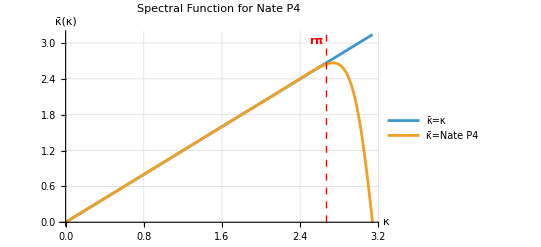

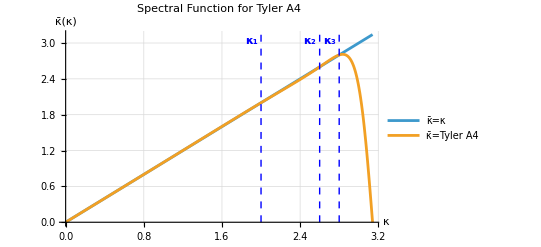

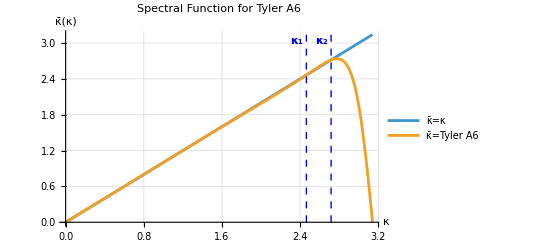

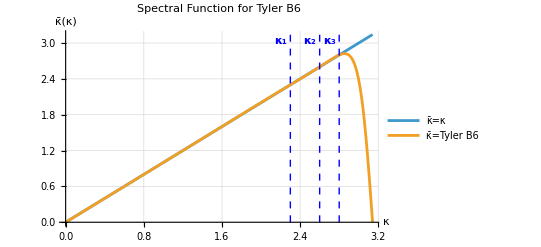

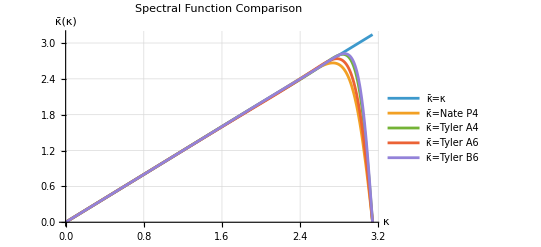

```mathematica
r=2.670/π;
Plot[{κ,κBar[κ]/.coeffsNateP4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Nate P4",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Nate P4"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffsTylerA4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Tyler A4",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A4"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA4[[1]],0},{κConstrA4[[1]],π}}],Text[Style["κ_1",Bold],{κConstrA4[[1]]-0.1,π-0.1}],Line[{{κConstrA4[[2]],0},{κConstrA4[[2]],π}}],Text[Style["κ_2",Bold],{κConstrA4[[2]]-0.1,π-0.1}],Line[{{κConstrA4[[3]],0},{κConstrA4[[3]],π}}],Text[Style["κ_3",Bold],{κConstrA4[[3]]-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffsTylerA6},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Tyler A6",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A6"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA6[[1]],0},{κConstrA6[[1]],π}}],Text[Style["κ_1",Bold],{κConstrA6[[1]]-0.1,π-0.1}],Line[{{κConstrA6[[2]],0},{κConstrA6[[2]],π}}],Text[Style["κ_2",Bold],{κConstrA6[[2]]-0.1,π-0.1}]}]

Plot[{κ,κBar2[κ]/.coeffsTylerB6},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Tyler B6",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler B6"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrB6[[1]],0},{κConstrB6[[1]],π}}],Text[Style["κ_1",Bold],{κConstrB6[[1]]-0.1,π-0.1}],Line[{{κConstrB6[[2]],0},{κConstrB6[[2]],π}}],Text[Style["κ_2",Bold],{κConstrB6[[2]]-0.1,π-0.1}],Line[{{κConstrB6[[3]],0},{κConstrB6[[3]],π}}],Text[Style["κ_3",Bold],{κConstrB6[[3]]-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffsNateP4,κBar[κ]/.coeffsTylerA4,κBar[κ]/.coeffsTylerA6,κBar2[κ]/.coeffsTylerB6},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function Comparison",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Nate P4","κ̄=Tyler A4","κ̄=Tyler A6","κ̄=Tyler B6"}]
```

# Filter Weighting

## A4 Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};

(*Optimization parameter*)
Δκ=0;

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Filter wavenumber*)
κc=r π+Δκ;
(*κc=0.6 π;*)
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Error integrand, Δ^2=(κD-N)^2*)
Δ2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

error=Integrate[Δ2[κ],{κ,0,r*π},Assumptions->0<r<1];
```

```mathematica
errorConstrained=error/.Solve[{fixedEq1,fixedEq2},{fixedPars[[1]],fixedPars[[2]]}][[1]];

(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[errorConstrained,freePars[[1]]]==0;
freeEq2=D[errorConstrained,freePars[[2]]]==0;
freeEq3=D[errorConstrained,freePars[[3]]]==0;

coeffsA4=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsA4//TableForm
```

{α→0.577046,β→0.0890084,a1→0.651708,a2→0.248159,a3→0.00600963}

α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963

## Error Integrals

```mathematica
ELow=Integrate[(Δ2[κ])/.coeffsA4,{κ,0,r*π}];
ETot=Integrate[(Δ2[κ])/.coeffsA4,{κ,0,π}];

Print[
TableForm[{
{"Low wavenumber: ",ScientificForm@ELow},
{"Total: ",ScientificForm@ETot}
}]]
```

Low wavenumber:  | 3.33808×10^-7
Total:  | 5.09089×10^-4

```mathematica
T[κ_]=1+(2*(a1*Cos[κ]+a2*Cos[2*κ]+a3*Cos[3*κ])-2*(a1+a2+a3))/(1+2*α*Cos[κ]+2*β*Cos[2*κ]);
(*T[κ_]=1+(2*(a1*(Cos[κ]-1)+a2*(Cos[2*κ]-1)+a3*(Cos[3*κ]-1)))/(1+2*α*Cos[κ]+2*β*Cos[2*κ])//FullSimplify*)

Aκc=30-5 Cos[κc]+10 Cos[2 κc]-3 Cos[3 κc];

αF=-(30 Cos[κc]+2 Cos[3 κc])/Aκc;
βF=(18+9 Cos[κc]+6 Cos[2 κc]-Cos[3 κc])/(2 Aκc);
a1F=30/Aκc (Cos[κc/2])^4;
a2F=-(2 a1F)/5;
a3F=a1F/15;

coeffsFilter={α->αF,β->βF,a1->a1F,a2->a2F,a3->a3F}
```

{α→0.662772,β→0.167446,a1→0.00219059,a2→-0.000876236,a3→0.000146039}

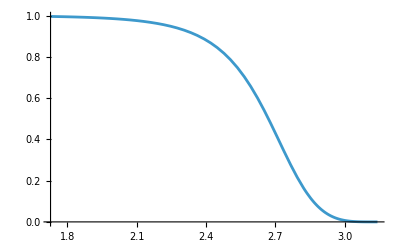

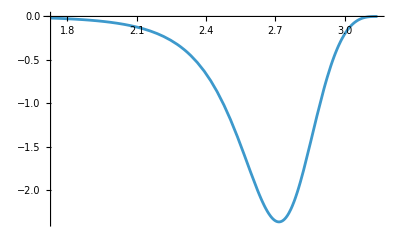

Low wavenumber:  | 2.87912×10^-7
Total:  | 4.83021×10^-6

```mathematica
Tp[κ_]=D[T[κ],κ];
Plot[T[κ]/.coeffsFilter,{κ,(r-0.3) π,π},PlotRange->All]
Plot[Tp[κ]/.coeffsFilter,{κ,(r-0.3) π,π},PlotRange->All]

ELowF=NIntegrate[((Δ2[κ])/.coeffsA4)*(T[κ]/.coeffsFilter),{κ,0,r*π}];
ETotF=NIntegrate[((Δ2[κ])/.coeffsA4)*(T[κ]/.coeffsFilter),{κ,0,π}];

Print[
TableForm[{
{"Low wavenumber: ",ScientificForm@ELowF},
{"Total: ",ScientificForm@ETotF}
}]]
```

## Optimization

```mathematica
ΔκList=Range[-1.40,0.45,0.05];
ETotList=Table[
(*Optimization parameter*)
Δκ=ΔκList[[i]];
(*Define the fractional wavenumber r*)
r=2.670/π;
(*Filter wavenumber*)
κc=r π+Δκ;


Aκc=30-5 Cos[κc]+10 Cos[2 κc]-3 Cos[3 κc];

αF=-(30 Cos[κc]+2 Cos[3 κc])/Aκc;
βF=(18+9 Cos[κc]+6 Cos[2 κc]-Cos[3 κc])/(2 Aκc);
a1F=30/Aκc (Cos[κc/2])^4;
a2F=-(2 a1F)/5;
a3F=a1F/15;

coeffsFilter={α->αF,β->βF,a1->a1F,a2->a2F,a3->a3F};



ETotF=NIntegrate[((Δ2[κ])/.coeffsA4)*(T[κ]/.coeffsFilter),{κ,0,π}];
ETotF=NIntegrate[((Δ2[κ])/.coeffsA4),{κ,r π,π}]-NIntegrate[((Δ2[κ])/.coeffsA4)*(T[κ]/.coeffsFilter),{κ,r π,π}];

{r,κc,Δκ,ETotF},
{i,1,Length@ΔκList}]
```

{{0.849887,1.27,-1.4,0.000508765},{0.849887,1.32,-1.35,0.000508764},{0.849887,1.37,-1.3,0.000508763},{0.849887,1.42,-1.25,0.000508761},{0.849887,1.47,-1.2,0.000508759},{0.849887,1.52,-1.15,0.000508757},{0.849887,1.57,-1.1,0.000508755},{0.849887,1.62,-1.05,0.000508752},{0.849887,1.67,-1.,0.000508748},{0.849887,1.72,-0.95,0.000508743},{0.849887,1.77,-0.9,0.000508737},{0.849887,1.82,-0.85,0.00050873},{0.849887,1.87,-0.8,0.000508721},{0.849887,1.92,-0.75,0.000508709},{0.849887,1.97,-0.7,0.000508694},{0.849887,2.02,-0.65,0.000508675},{0.849887,2.07,-0.6,0.00050865},{0.849887,2.12,-0.55,0.000508617},{0.849887,2.17,-0.5,0.000508574},{0.849887,2.22,-0.45,0.000508516},{0.849887,2.27,-0.4,0.000508438},{0.849887,2.32,-0.35,0.000508332},{0.849887,2.37,-0.3,0.000508186},{0.849887,2.42,-0.25,0.00050798},{0.849887,2.47,-0.2,0.000507686},{0.849887,2.52,-0.15,0.000507259},{0.849887,2.57,-0.1,0.000506629},{0.849887,2.62,-0.05,0.000505678},{0.849887,2.67,2.22045×10^-16,0.000504213},{0.849887,2.72,0.05,0.000501911},{0.849887,2.77,0.1,0.000498219},{0.849887,2.82,0.15,0.000492183},{0.849887,2.87,0.2,0.000482128},{0.849887,2.92,0.25,0.000465071},{0.849887,2.97,0.3,0.000435605},{0.849887,3.02,0.35,0.00038372},{0.849887,3.07,0.4,0.00029034},{0.849887,3.12,0.45,0.000117356}}

# Second Derivatives

# P4 (A4) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF) (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

4

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2/(2!)*(a1+2^2*a2+3^2*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(4!)*(a1+2^4*a2+3^4*a3);



(*We define the numerator, denominator, and spectral function*)
(*Num[κ_]=2*(a1+a2+a3)-2*(a1*Cos[κ]+a2*Cos[2*κ]+a3*Cos[3*κ]);*)
Num[κ_]=4*(a1*(Sin[κ/2])^2+a2*(Sin[(2*κ)/2])^2+a3*(Sin[(3*κ)/2])^2);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];



(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ^2*Denom[κ]-Num[κ])^2//Expand;
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
EDHConstr=EDH/.Solve[{fixedEq1,fixedEq2},{fixedPars[[1]],fixedPars[[2]]}][[1]];



(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDHConstr,freePars[[1]]]==0;
freeEq2=D[EDHConstr,freePars[[2]]]==0;
freeEq3=D[EDHConstr,freePars[[3]]]==0;

coeffsNateA42nd=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsNateA42nd//TableForm
```

{α→0.491759,β→0.0521073,a1→0.24561,a2→0.421123,a3→0.0175146}

α→0.491759
β→0.0521073
a1→0.24561
a2→0.421123
a3→0.0175146

## Visualization

idk if this is useful, but the constraint it must satisfy is:
	κ̃(0)=0
κ̃(π)=(4(a_1+a_3))/(1-2α+2β)
also be sure to rename to kappa tilde instead of kappabar if you want to stay consistent

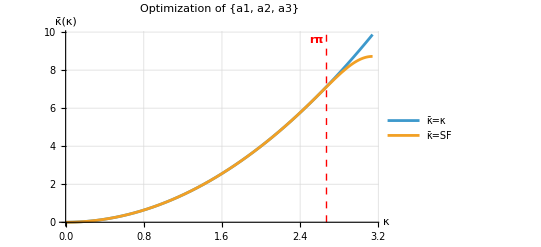

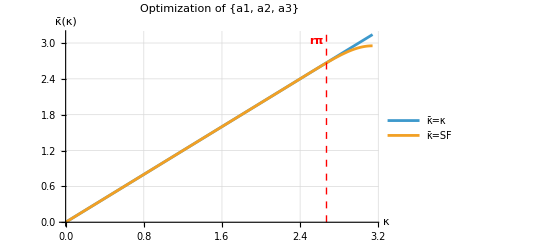

```mathematica
Plot[{κ^2,κBar[κ]/.coeffsNateA42nd},{κ,0,π},PlotRange->{0,π^2},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2-0.3}]}]
Plot[{κ,Sqrt[κBar[κ]/.coeffsNateA42nd]},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

## Spectral

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};
(*This should be the same length as freePars*)
κConstrA42nd={2.0,2.6,2.8};
```

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2/(2!)*(a1+2^2*a2+3^2*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(4!)*(a1+2^4*a2+3^4*a3);
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
(*Num[κ_]=2*(a1+a2+a3)-2*(a1*Cos[κ]+a2*Cos[2*κ]+a3*Cos[3*κ]);*)
Num[κ_]=4*(a1*(Sin[κ/2])^2+a2*(Sin[(2*κ)/2])^2+a3*(Sin[(3*κ)/2])^2);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num[κConstrA42nd[[1]]]==(κConstrA42nd[[1]])^2*Denom[κConstrA42nd[[1]]];
freeEq2=Num[κConstrA42nd[[2]]]==(κConstrA42nd[[2]])^2*Denom[κConstrA42nd[[2]]];
freeEq3=Num[κConstrA42nd[[3]]]==(κConstrA42nd[[3]])^2*Denom[κConstrA42nd[[3]]];

coeffsTylerA42nd=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffsTylerA42nd//TableForm
```

{α→0.524845,β→0.0632013,a1→0.148951,a2→0.453071,a3→0.023873}

α→0.524845
β→0.0632013
a1→0.148951
a2→0.453071
a3→0.023873

```mathematica
Plot[{κ^2,κBar[κ]/.coeffsTylerA42nd},{κ,0,π},PlotRange->{0,π^2},PlotLabel->"Spectral Function for Tyler A4",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A4"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA42nd[[1]],0},{κConstrA42nd[[1]],π^2}}],Text[Style["κ_1",Bold],{κConstrA42nd[[1]]-0.1,π^2-0.3}],Line[{{κConstrA42nd[[2]],0},{κConstrA42nd[[2]],π^2}}],Text[Style["κ_2",Bold],{κConstrA42nd[[2]]-0.1,π^2-0.3}],Line[{{κConstrA42nd[[3]],0},{κConstrA42nd[[3]],π^2}}],Text[Style["κ_3",Bold],{κConstrA42nd[[3]]-0.1,π^2-0.3}]}]
Plot[{κ,Sqrt[κBar[κ]/.coeffsTylerA42nd]},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Tyler A4",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A4"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA42nd[[1]],0},{κConstrA42nd[[1]],π}}],Text[Style["κ_1",Bold],{κConstrA42nd[[1]]-0.1,π-0.1}],Line[{{κConstrA42nd[[2]],0},{κConstrA42nd[[2]],π}}],Text[Style["κ_2",Bold],{κConstrA42nd[[2]]-0.1,π-0.1}],Line[{{κConstrA42nd[[3]],0},{κConstrA42nd[[3]],π}}],Text[Style["κ_3",Bold],{κConstrA42nd[[3]]-0.1,π-0.1}]}]
```

-Graphics-

-Graphics-

### Error comparison with Kim-style optimization

```mathematica
r=2.670/π;

ELowNateA4=Integrate[(ΔDH2[κ])/.coeffsNateA42nd,{κ,0,r*π}];
ELowTylerA4=Integrate[(ΔDH2[κ])/.coeffsTylerA42nd,{κ,0,r*π}];

ETotNateA4=Integrate[(ΔDH2[κ])/.coeffsNateA42nd,{κ,0,π}];
ETotTylerA4=Integrate[(ΔDH2[κ])/.coeffsTylerA42nd,{κ,0,π}];

Print[
"Integrated error for low wavenumber (κ≤rπ):\n",
TableForm[{
{"Nate P4:",ScientificForm@ELowNateA4},
{"Tyler A4:",ScientificForm@ELowTylerA4}
}]]
Print[
"Integrated total error:\n",
TableForm[{
{"Nate P4:",ScientificForm@ETotNateA4},
{"Tyler A4:",ScientificForm@ETotTylerA4}
}]]
```

Integrated error for low wavenumber (κ≤rπ):
Nate P4: | 4.49717×10^-7
Tyler A4: | 4.72932×10^-6

Integrated total error:
Nate P4: | 1.58551×10^-3
Tyler A4: | 2.65021×10^-4

# P6 (A6) Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF) (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β,a1};
freePars={a2,a3};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

6

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2/(2!)*(a1+2^2*a2+3^2*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(4!)*(a1+2^4*a2+3^4*a3);
fixedEq3=2/(4!)*(α+2^4*β)==2/(6!)*(a1+2^6*a2+3^6*a3);



(*We define the numerator, denominator, and spectral function*)
(*Num[κ_]=2*(a1+a2+a3)-2*(a1*Cos[κ]+a2*Cos[2*κ]+a3*Cos[3*κ]);*)
Num[κ_]=4*(a1*(Sin[κ/2])^2+a2*(Sin[(2*κ)/2])^2+a3*(Sin[(3*κ)/2])^2);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];



(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ^2*Denom[κ]-Num[κ])^2//Expand;
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
EDHConstr=EDH/.Solve[{fixedEq1,fixedEq2},{fixedPars[[1]],fixedPars[[2]]}][[1]];



(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDHConstr,freePars[[1]]]==0;
freeEq2=D[EDHConstr,freePars[[2]]]==0;

coeffsNateA62nd=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2},{α,β,a1,a2,a3}][[1]]
coeffsNateA62nd//TableForm
```

{α→0.463117,β→0.0428503,a1→0.329437,a2→0.392885,a3→0.0123286}

α→0.463117
β→0.0428503
a1→0.329437
a2→0.392885
a3→0.0123286

## Visualization

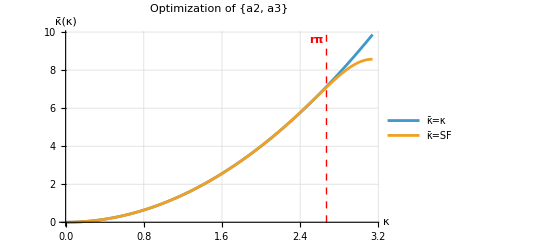

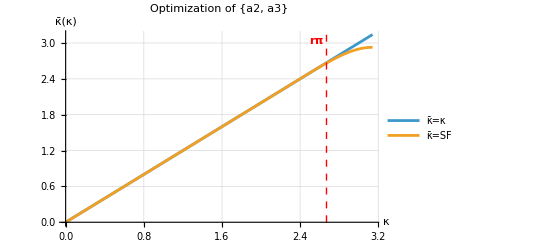

```mathematica
Plot[{κ^2,κBar[κ]/.coeffsNateA62nd},{κ,0,π},PlotRange->{0,π^2},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2-0.3}]}]
Plot[{κ,Sqrt[κBar[κ]/.coeffsNateA62nd]},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

## Spectral

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β,a1};
freePars={a2,a3};
(*This should be the same length as freePars*)
κConstrA62nd={2.6,2.8};
```

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2/(2!)*(a1+2^2*a2+3^2*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(4!)*(a1+2^4*a2+3^4*a3);
fixedEq3=2/(4!)*(α+2^4*β)==2/(6!)*(a1+2^6*a2+3^6*a3);
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
(*Num[κ_]=2*(a1+a2+a3)-2*(a1*Cos[κ]+a2*Cos[2*κ]+a3*Cos[3*κ]);*)
Num[κ_]=4*(a1*(Sin[κ/2])^2+a2*(Sin[(2*κ)/2])^2+a3*(Sin[(3*κ)/2])^2);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=Num[κConstrA62nd[[1]]]==(κConstrA62nd[[1]])^2*Denom[κConstrA62nd[[1]]];
freeEq2=Num[κConstrA62nd[[2]]]==(κConstrA62nd[[2]])^2*Denom[κConstrA62nd[[2]]];

coeffsTylerA62nd=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2},{α,β,a1,a2,a3}][[1]]
coeffsTylerA62nd//TableForm
```

{α→0.503756,β→0.0535599,a1→0.20587,a2→0.438439,a3→0.0172228}

α→0.503756
β→0.0535599
a1→0.20587
a2→0.438439
a3→0.0172228

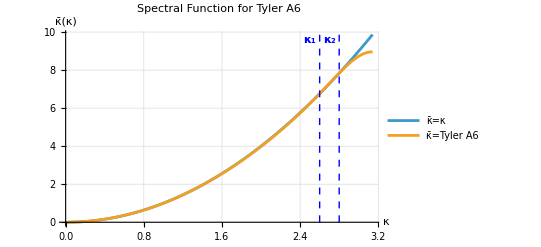

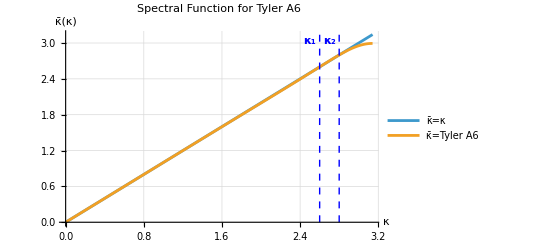

```mathematica
Plot[{κ^2,κBar[κ]/.coeffsTylerA62nd},{κ,0,π},PlotRange->{0,π^2},PlotLabel->"Spectral Function for Tyler A6",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A6"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA62nd[[1]],0},{κConstrA62nd[[1]],π^2}}],Text[Style["κ_1",Bold],{κConstrA62nd[[1]]-0.1,π^2-0.3}],Line[{{κConstrA62nd[[2]],0},{κConstrA62nd[[2]],π^2}}],Text[Style["κ_2",Bold],{κConstrA62nd[[2]]-0.1,π^2-0.3}]}]
Plot[{κ,Sqrt[κBar[κ]/.coeffsTylerA62nd]},{κ,0,π},PlotRange->{0,π},PlotLabel->"Spectral Function for Tyler A6",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=Tyler A6"},Epilog->{Directive[{Thick,Blue,Dashed}],Line[{{κConstrA62nd[[1]],0},{κConstrA62nd[[1]],π}}],Text[Style["κ_1",Bold],{κConstrA62nd[[1]]-0.1,π-0.1}],Line[{{κConstrA62nd[[2]],0},{κConstrA62nd[[2]],π}}],Text[Style["κ_2",Bold],{κConstrA62nd[[2]]-0.1,π-0.1}]}]
```

### Error comparison with Kim-style optimization

```mathematica
r=2.670/π;

ELowNateA6=Integrate[(ΔDH2[κ])/.coeffsNateA62nd,{κ,0,r*π}];
ELowTylerA6=Integrate[(ΔDH2[κ])/.coeffsTylerA62nd,{κ,0,r*π}];

ETotNateA6=Integrate[(ΔDH2[κ])/.coeffsNateA62nd,{κ,0,π}];
ETotTylerA6=Integrate[(ΔDH2[κ])/.coeffsTylerA62nd,{κ,0,π}];

Print[
"Integrated error for low wavenumber (κ≤rπ):\n",
TableForm[{
{"Nate A6:",ScientificForm@ELowNateA6},
{"Tyler A6:",ScientificForm@ELowTylerA6}
}]]
Print[
"Integrated total error:\n",
TableForm[{
{"Nate A6:",ScientificForm@ETotNateA6},
{"Tyler A6:",ScientificForm@ETotTylerA6}
}]]
```

Integrated error for low wavenumber (κ≤rπ):
Nate A6: | 3.02951×10^-6
Tyler A6: | 4.60817×10^-5

Integrated total error:
Nate A6: | 3.96653×10^-3
Tyler A6: | 5.65637×10^-4